# Square wave

```mathematica
Clear["Global`*"]
```

### Trigonometric Representation

```mathematica
Period=1;
```

```mathematica
Subscript[y, Min]=-1;
```

```mathematica
Subscript[y, Max]=1;
```

```mathematica
f=SquareWave[{Subscript[y, Min],Subscript[y, Max]},x/Period];
```

```mathematica
fs=FourierTrigSeries[f,x,10,FourierParameters->{1,(2π)/Period}]
```

(4 Sin[2 π x])/π+(4 Sin[6 π x])/(3 π)+(4 Sin[10 π x])/(5 π)+(4 Sin[14 π x])/(7 π)+(4 Sin[18 π x])/(9 π)

```mathematica
list1=List@@Normal[fs]
```

{(4 Sin[2 π x])/π,(4 Sin[6 π x])/(3 π),(4 Sin[10 π x])/(5 π),(4 Sin[14 π x])/(7 π),(4 Sin[18 π x])/(9 π)}

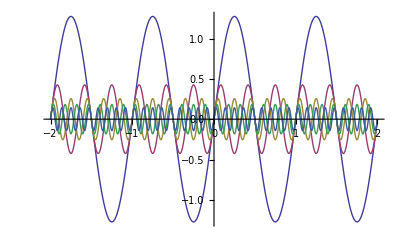

```mathematica
Plot[list1,{x,-2,2}]
```

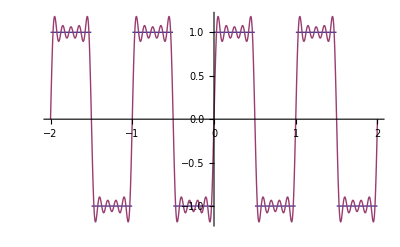

```mathematica
Plot[{f,fs}, {x,-2Period,2Period},PlotRange -> All]
```

### Complex Representation

```mathematica
Clear["Global`*"]
```

The spectral density function

```mathematica
g[k_]:=8/k
```

```mathematica
Table[g[k],{k,2π,20π,4π}]
```

{4/π,4/(3 π),4/(5 π),4/(7 π),4/(9 π)}

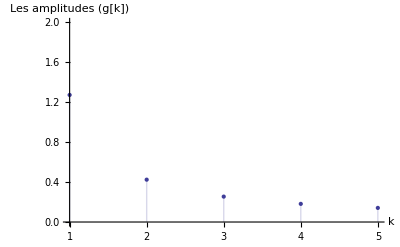

```mathematica
ListPlot[Table[g[k],{k,2π,20π,4π}],Filling->Axis,PlotRange->{0,2},AxesLabel->{"k","Les amplitudes (g[k])"}]
```

```mathematica
f[x_]=Sum[g[k] ⅇ^(ⅈ k x),{k,2π,20π,4π}]
```

(4 ⅇ^(2 ⅈ π x))/π+(4 ⅇ^(6 ⅈ π x))/(3 π)+(4 ⅇ^(10 ⅈ π x))/(5 π)+(4 ⅇ^(14 ⅈ π x))/(7 π)+(4 ⅇ^(18 ⅈ π x))/(9 π)

```mathematica
list2=Table[g[k] ⅇ^(ⅈ k x),{k,2π,20π,4π}]
```

{(4 ⅇ^(2 ⅈ π x))/π,(4 ⅇ^(6 ⅈ π x))/(3 π),(4 ⅇ^(10 ⅈ π x))/(5 π),(4 ⅇ^(14 ⅈ π x))/(7 π),(4 ⅇ^(18 ⅈ π x))/(9 π)}

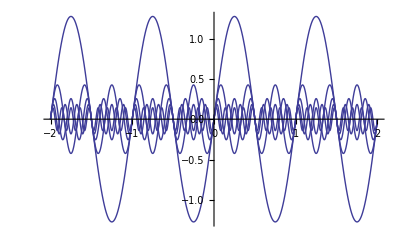

```mathematica
Plot[Im[list2],{x,-2,2}]
```

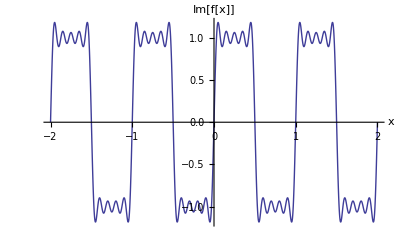

```mathematica
Plot[Im[f[x]],{x,-2,2},AxesLabel->{"x","Im[f[x]]"}]
```

### Play

```mathematica
Play[Im[f[300x]],{x,0,3}]
```

-Graphics-